```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

# LASSO with AIC, AICc, and BIC

This y(x) is a “theory” curve used to generate pseudo data. We’ll check if LASSO in combination with AIC, AICc, or BIC is capable of reconstructing this input.

```mathematica
y[x_]=2+0.5*x-0.1*(x-5.)^2+0.4*Sin[x];
```

### Data generation:

Next, we generate pseudo-data that scatter around the theory curve normally distributed.

```mathematica
max=14; (* generate data from x=0 to x=max *)
delta=.25; (* Distance between data points *)
sigma=.12; (* Data uncertainty *)
raerr=RandomVariate[NormalDistribution[0,sigma],Floor[max/delta+4]];
datnoerr=Table[{x,y[x]},{x,0,max,delta}];
le=Length[datnoerr];(* No of data points generated *)
data=Table[{datnoerr[[i,1]],datnoerr[[i,2]]+raerr[[i]]},{i,1,le}];
(* Table that stores the pseudo-data *)
```

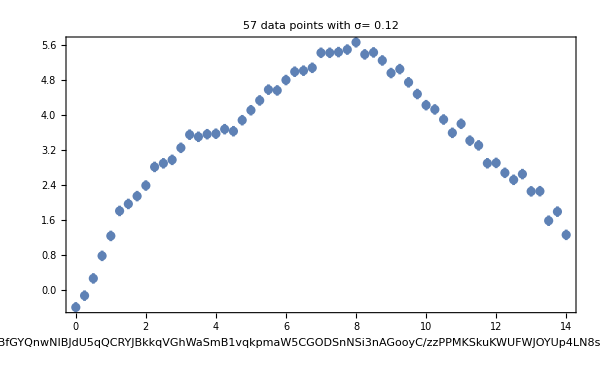

```mathematica
tabforplot=Table[{{data[[i,1]],data[[i,2]]},ErrorBar[sigma]},{i,1,le}];
elp=ErrorListPlot[tabforplot,Frame->True,FrameLabel->{Style["x",Medium],Style["y(x)",Medium]},PlotLabel->Style[ToString[le]<>" data points with σ= "<>ToString[sigma],Large],ImageSize->600]
```

We fit these data now with a simple function that contains the correct solution, but has more terms. The question is: Can we reconstruct the original model? This is called model selection. LASSO + some criterion should give us an answer.

For this, we write for a fit of m+1 parameters a[0],...,a[mmax]. As you see, we use for the fit ansatz Legendre polynomials instead of ordinary ones. This simply reduces the correlations of fit parameters because the Legendre polynomials are constructed such that they are orthogonal over the considered fit interval. We also add not only the sin-function as a possible term, but also a cos function, just the heck of it.

```mathematica
mmax=20;
ho[x_]=Sum[a[i]LegendreP[i,(x-max/2)/(max/2)],{i,0,mmax-2}]+a[mmax-1]*Sin[x]+a[mmax]*Cos[x]; (* Fit polynomial of degree n. This is the Null hypothesis *)
```

Exercise 1) Fit with mmax parameters, calculate the χ^2, and quote the χ^2/d.o.f. Show result together with data.

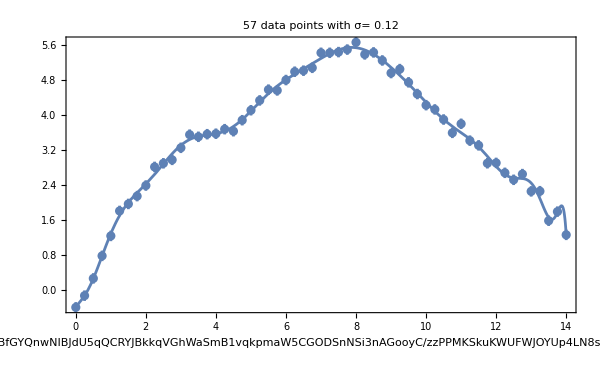

χ^2 is: 28.4384

χ_(d . o . f .)=χ^2/(#data-#parameters) is: 0.789955

```mathematica
parms=Table[a[i],{i,0,mmax}]; (* Table of parameters, needed for Findminimum *)
chisq=Sum[(ho[data[[i,1]]]-data[[i,2]])^2/sigma^2,{i,1,le}]; (* Definition of the χ^2 to be minimized in nect step *)
tmp=FindMinimum[chisq,parms];
chisqq=tmp[[1]]; (* Fit result; first argument is the χ^2 *)
bestparm=tmp[[2]];(* Second argument is a replacement list for best parameter values *)
Show[elp,Plot[ho[x]/.bestparm,{x,0,max},ImageSize->600]]
Print["χ^2 is: ", chisqq]
Print["χ_(d . o . f .)=χ^2/(#data-#parameters) is: ",chisqq/(le-(mmax+1))," "]
```

```mathematica
-Graphics--Graphics-
```

-Graphics- -Graphics-

### Try to split data in training set and validation set

Divide the data set randomly in 70% training set and 30% validation set. Our data file is:

```mathematica
sigma
```

0.12

```mathematica
le
```

57

```mathematica
le=Length[data]
```

57

```mathematica
57
```

57

```mathematica
data
```

{{0.,-0.391377},{0.25,-0.124012},{0.5,0.270151},{0.75,0.785928},{1.,1.24212},{1.25,1.81353},{1.5,1.97353},{1.75,2.15255},{2.,2.39451},{2.25,2.8201},{2.5,2.90281},{2.75,2.98172},{3.,3.25704},{3.25,3.55761},{3.5,3.50905},{3.75,3.56859},{4.,3.57952},{4.25,3.68323},{4.5,3.63691},{4.75,3.88867},{5.,4.11643},{5.25,4.34091},{5.5,4.58734},{5.75,4.56953},{6.,4.80721},{6.25,4.99736},{6.5,5.0213},{6.75,5.08678},{7.,5.43002},{7.25,5.42992},{7.5,5.44619},{7.75,5.50388},{8.,5.67021},{8.25,5.39356},{8.5,5.43871},{8.75,5.25485},{9.,4.96712},{9.25,5.05739},{9.5,4.75468},{9.75,4.48751},{10.,4.23261},{10.25,4.13492},{10.5,3.90424},{10.75,3.59943},{11.,3.80649},{11.25,3.42098},{11.5,3.31302},{11.75,2.90381},{12.,2.91206},{12.25,2.68509},{12.5,2.52548},{12.75,2.65595},{13.,2.26114},{13.25,2.26516},{13.5,1.58976},{13.75,1.79739},{14.,1.26658}}

How to access data: Lets access the first and third element of that list:

```mathematica
data[[1]]
data[[3]]
```

{0.,-0.391377}

{0.5,0.270151}

How to make a list longer: For example, combine these two data points into a new list, say, training data:

By Hand (recommended)

```mathematica
training={data[[1]], data[[3]]}
```

{{0.,-0.391377},{0.5,0.270151}}

Better: Automatically, by AppenTo

```mathematica
training={};
tmp=AppendTo[training,data[[1]]];
AppendTo[tmp,data[[3]]]
```

{{0.,-0.391377},{0.5,0.270151}}

Automatize this with a do loop:

```mathematica
training={};
Do[AppendTo[training,data[[i]]],{i,1,3}]
training
```

{{0.,-0.391377},{0.25,-0.124012},{0.5,0.270151}}

Next, we need to divide the above data set into 70% trainig and 30% validation, in a random way!!! Hints:

```mathematica
RandomReal[]
```

0.0978903

```mathematica
RandomInteger[{1,le}]
```

7

Question to you: How can I use that to make random decision for the desired splitting of my data set? Second hint: I need to have some If - then - else structure in combination with that random number. If, then else works like this in Mathematica:

```mathematica
If[1==1,Print["True"],Print["False"]]
```

True

And, finally, this kind of construction should run over the entire data list. So, this should appear in combination with a do or for loop.

```mathematica
training={};
validation={};
SeventhPer=0.7*Length[data];
ThirthPer=0.3*Length[data];


Do[If[RandomReal[]< 0.7 ,AppendTo[training,data[[i]]],AppendTo[validation,data[[i]]]],{i,1,le}]
(*training
validation*)
Length[training]
Length[validation]
(*Get the chi-square of the validation set*)

ChiofValid=Sum[(ho[validation[[i,1]]]-validation[[i,2]])^2/sigma^2,{i,1,Length[validation]}];
ChiofTraining=Sum[(ho[training[[i,1]]]-training[[i,2]])^2/sigma^2,{i,1,Length[training]}];
mmax=20;
parms=Table[a[i],{i,0,mmax}] (* Table of parameters, needed for Findminimum *);
aReal = {1,1,1,1}; (* Some initial value *)
parvalue = Table[{parms[[i]],If[i≤4,aReal[[i]],0]},{i,1,mmax+1}]; (*initial values for fit parameters*)

(*Replace the fit parameters in our expression with the numerical values obtained in the fit to the training set. Like in "Findminimum" is a replacement list. Save that under a new name and append it to our expression ChipofValid we will have one numerical number   append attach smt*)

tmp= FindMinimum[ChiofTraining,parvalue] ;
bestparm=tmp[[2]];

chisqq=tmp[[1]];


ChiofValid/.bestparm
fitted[x_] = Simplify[ho[x] /. bestparm] 
(aa[0] + aa[1]) /. {aa[0] -> 1., aa[1] -> 2.}
chival = Sum[(fitted[validation[[i, 1]]] - validation[[i, 2]])^2/sigma^2, {i, 
   1, Length[validation]}]
fitplot = Plot[fitted[x], {x, data[[1, 1]], data[[le, 1]]}];
Show[ListPlot[{training, validation}, PlotLegends -> {"Training", "Validation"}, Frame -> True], fitplot]
```

36

21

7486.57

-1.95161×10^6-2.26663×10^6 x+976073. x^2+377009. x^3-80116.3 x^4-20105.8 x^5+3556. x^6+28.8716 x^7+106.551 x^8-49.3412 x^9+9.70828 x^10-1.44475 x^11+0.184729 x^12-0.018389 x^13+0.0012958 x^14-0.0000614385 x^15+1.8641×10^-6 x^16-3.27931×10^-8 x^17+2.55356×10^-10 x^18+1.95161×10^6 Cos[x]+2.26659×10^6 Sin[x]

3.

7488.65

-Graphics-

```mathematica
Print["Training X^2=  ", chisqq]
Print["Validation X^2=  ", chival]
```

Training X^2=  9.22949

Validation X^2=  7488.65

```mathematica
Print["Training X^2 per training data point= ", chisqq/Length[training]]
Print["Validation X^2 per validation data point= ", chival/Length[validation]]
```

Training X^2 per training data point= 0.256375

Validation X^2 per validation data point= 356.603

```mathematica
validation
```

{{0.25,-0.124012},{1.,1.24212},{1.5,1.97353},{1.75,2.15255},{2.25,2.8201},{2.5,2.90281},{2.75,2.98172},{3.,3.25704},{3.25,3.55761},{4.5,3.63691},{5.5,4.58734},{6.,4.80721},{6.75,5.08678},{7.5,5.44619},{8.75,5.25485},{9.,4.96712},{9.25,5.05739},{11.5,3.31302},{12.,2.91206},{13.,2.26114},{14.,1.26658}}

# K-fold cross validation

```mathematica
validate={};
Monitor[Do[penalty=λ^4*Sum[Abs[a[j] ],{j,0,mmax}];
ChiofTraining=Sum[(ho[training[[i,1]]]-training[[i,2]])^2/sigma^2,{i,1,Length[training]}]+penalty;
tmp=FindMinimum[ChiofTraining,parvalue]//Quiet;
bestparm=tmp[[2]];
parvalue=Table[{parms[[i]],bestparm[[i,2]]},{i,1,mmax+1}];
fitted[x_]=Simplify[ho[x]/.bestparm];
chival=Sum[(fitted[validation[[i,1]]]-validation[[i,2]])^2/sigma^2,{i,1,Length[validation]}];AppendTo[validate,{λ,chival}],{λ,6,0,-0.5}],λ]
```

```mathematica
validate
```

{{6.,782.843},{5.5,652.219},{5.,260.203},{4.5,163.009},{4.,55.2075},{3.5,32.3022},{3.,21.5233},{2.5,18.5588},{2.,20.0107},{1.5,35.9786},{1.,147.937},{0.5,1534.46},{0.,7486.88}}

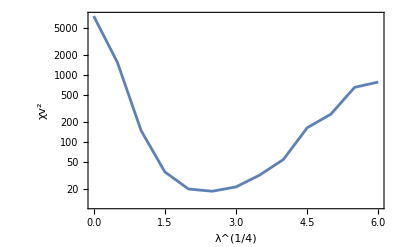

```mathematica
(*ListLogPlot[validate,Joined->True,Frame->True,FrameLabel->{MaTeX["λ^{1/4}"],"Xv^2"} ]
ListLogPlot[validate, Joined -> True, Frame -> True, 
 FrameLabel -> {"\!\(\*SuperscriptBox[\(λ\), \(1/4\)]\)", 
   "\!\(\*SuperscriptBox[\(χv\), \(2\)]\)"} ]*)
(*ListLogPlot[validate,Joined->True,Frame->True,FrameLabel->{SuperscriptBox[λ,1/4],"Xv^2"} ]*)
ListLogPlot[validate, Joined -> True, Frame -> True, 
 FrameLabel -> {"\!\(\*SuperscriptBox[\(λ\), \(1/4\)]\)", 
   "\!\(\*SuperscriptBox[\(χv\), \(2\)]\)"} ]
```

To find the maximally regularized we use (1-σ) rule
(1-σ)  rule:
-Graphics-

```mathematica
Clear[i,k,training,validation]
Kf=5;
Randint=RandomInteger[{1,Kf},le];
Do[validation[k]={},{k,1,Kf}];
Do[AppendTo[validation[Randint[[i]]],data[[i]]],{i,1,le}]
Do[training[k]=Complement[data,validation[k]],{k,1,Kf}]
```

-Graphics-

```mathematica
kfoldchi={}; Clear[chival]
penalty=λ^4*Sum[Abs[a[j] ],{j,0,mmax}];
Monitor[Do[Do[ChiofTraining=Sum[(ho[training[k][[i,1]]]-training[k][[i,2]])^2/sigma^2,{i,1,Length[training[k]]}]+penalty;
tmp=FindMinimum[ChiofTraining,parvalue]//Quiet;
chisqq=tmp[[1]];
bestparm=tmp[[2]];
parvalue=Table[{parms[[i]],bestparm[[i,2]]},{i,1,mmax+1}];
fitted[x_]=Simplify[ho[x]/.bestparm];
chival[k]=Sum[(fitted[validation[k][[i,1]]]-validation[k][[i,2]])^2/sigma^2,{i,1,Length[validation[k]]}];
chibark[k]=chival[k]/Length[validation[k]],{k,1.Kf}];
chibar=1/le*Sum[chival[k],{k,1,Kf}];
Δ=Sqrt[1./(Kf-1)Sum[(chibark[k]-chibar)^2,{k,1,Kf}]]/Sqrt[Kf];
AppendTo[kfoldchi,{λ,chibar,Δ}],{λ,6,0,-0.5}],λ]
```

```mathematica
ListPlot[Table[{kfoldchi[[lam,1]],Around[kfoldchi[[lam,2]],kfoldchi[[lam,3]]]},{lam,1,Length[kfoldchi]}],Joined->True,PlotRange->{0,3},Frame->True,FrameLabel->{"\!\(\*SuperscriptBox[\(λ\), \(1/4\)]\)", 
   "\!\(\*SuperscriptBox[\(χv\), \(2\)]\)"} ]
```

-Graphics-

Finding the minimum position to next apply the 1-σ

```mathematica
MinimalPosition=Position[kfoldchi[[All,2]],Min[kfoldchi[[All,2]]]][[1,1]]
```

8

```mathematica
Position[{-1,-2,4,3},4][[1,1]]
```

3

calculate X^2+Δ at the minimum

```mathematica
chiplusone=Min[kfoldchi[[All,2]]]+kfoldchi[[MinimalPosition,3]]
```

1.37761

```mathematica
Show[ListPlot[Table[{kfoldchi[[lam,1]],Around[kfoldchi[[lam,2]],kfoldchi[[lam,3]]]},{lam,1,Length[kfoldchi]}],Joined->True,PlotRange->{0,3}],Plot[chiplusone,{x,kfoldchi[[MinimalPosition,1]],5},PlotStyle->Red],Frame->True,FrameLabel->{"\!\(\*SuperscriptBox[\(λ\), \(1/4\)]\)", 
   "\!\(\*SuperscriptBox[\(χv\), \(2\)]\)"} ]
```

-Graphics-

```mathematica
interchi=Interpolation[Table[{kfoldchi[[lam,1]],kfoldchi[[lam,2]]},{lam,1,Length[kfoldchi]}],InterpolationOrder->1];
Print["The 1-σ rule predicts λ= ",largerlam=FindRoot[interchi[x]== chiplusone,{x,kfoldchi[[MinimalPosition,1]]+1.}][[1,2]]]
```

The 1-σ rule predicts λ= 3.08153

```mathematica
Show[ListPlot[Table[{kfoldchi[[lam,1]],Around[kfoldchi[[lam,2]],kfoldchi[[lam,3]]]},{lam,1,Length[kfoldchi]}],PlotRange->{0,3}],Plot[{chiplusone},{x,kfoldchi[[MinimalPosition,1]],largerlam},PlotStyle->{Red}],Plot[interchi[x],{x,0,6},PlotStyle->{Blue}],Graphics[{Red,Line[{{largerlam,0},{largerlam,chiplusone}}]}],Frame->True,FrameLabel->{"\!\(\*SuperscriptBox[\(λ\), \(1/4\)]\)", 
   "\!\(\*SuperscriptBox[\(χv\), \(2\)]\)"}]
```

-Graphics-

### Exercises 2 to end

Exercise 2) Set mmax=20, i.e., construct a model that has the capability to wildly over-fit the data. 
a) Add a penalty to the normal χ of the form Δχ= λ∑|a|. The power 4 for the λ-term doesn’t change anything, it just makes the minima in the later plots of AIC etc. more symmetric and more visible.
b) Scan values of λ from λ=7 to λ=0, with Δλ=-0.1, i.e., you start with a LARGE λ and work your way down to λ=0. For each value of λ, record the set of best fit parameters and use it as starting point for the fit at the next value at λ-Δλ. This is a simple way of avoiding instabilities in the fit, i.e., fits that simply don’t converge well. The “updating” of start values for the fit can in principle be skipped if LASSO is implemented in a bit more elaborated way than we are doing it here (e.g., least angle regression).
c) Later, you will need, for each value of λ, the value of χ (that is the χ WITHOUT the penalty term) and the number of parameters. Record both for later analysis. Note: We count here a parameter being zero, IF |a|<0.01. As mentioned in class, that threshold introduces some arbitrariness in the problem. It can be altogether avoided by calculating the number of fit parameters as the covariance between data and fit. However, that requires additional programming effort which we want to avoid here. So simply take that threshold.
d) For each λ, save also a plot that shows the corresponding fit together with the data to make an animation (next exercise).
e) Also, for each λ, you have to store the list of non-zero parameters so in the end you know which ones are the important ones.

```mathematica
(*Fitting model is the polynomial of the power mmax: *)
mmax=20;
parms=Table[a[i],{i,0,mmax}] (* Table of parameters, needed for Findminimum *);
```

```mathematica
(*loop over all lambda values: *)
Clear[lambda];
icount=1;
chinoplist={}; (*data list to save chi square as a function of lambda *)
palist={};
nopalist={};
aReal = {1,1,1,1}; (* Some initial value *)
parvalue = Table[{parms[[i]],If[i≤4,aReal[[i]],0]},{i,1,mmax+1}]; (*initial values for fit parameters*)

Do[
 chisq = 
   Sum[(ho[data[[i, 1]]] - data[[i, 2]])^2/sigma^2, {i, 1, le}] + 
    lambda^4*Sum[Abs[a[i]], {i, 0, mmax}] ;
tmp=FindMinimum[chisq,parvalue]//Quiet;
chisqq=tmp[[1]]; (* Fit result; first argument is the X^2 *)
bestparm=tmp[[2]]; (* Second argument is a replacement list for best parameter values *)
parvalue = Table[{parms[[i]],bestparm[[i,2]]},{i,1,mmax+1}]; (*update parameters value*) 
chinopenalty=Sum[((ho[data[[i,1]]]/.bestparm)-data[[i,2]])^2/sigma^2,{i,1,le}];
kkcount=1; (*This and next 2 lines: Count the number of non-zero parameters; note: sigma ^2 counts as additional parameter*)
Do[If[Abs[bestparm[[i,2]]]>0.01,kkcount=kkcount+1],{i,1,mmax+1}];
AppendTo[nopalist,{lambda,kkcount}];
plotl[icount]=Show[elp,Plot[ho[x]/.bestparm,{x,0,max},PlotRange->All,PlotStyle->Red,ImageSize->600]];
plotlAll[icount] = Row[{plotl[icount],Style[" Lambda: "<>ToString[lambda], Large]}]; 
icount=icount+1;(* AppendTo[chilist,{lambda,chisqq}];*) (* Record X^2 with penalty*)
AppendTo[chinoplist,{lambda,chinopenalty}];(* Record X^2 without penalty; important for AIC*)
AppendTo[palist,{lambda,bestparm[[;;,2]]}](* Record parameter values *),{lambda,7,0,-.1}]
```

Exercise 3) Using ListAnimate, show the graphical outcome of the fit as a function of λ.

```mathematica
(*Animation of how fit is changed with lambda: *)
ListAnimate[Table[plotlAll[i],{i,1,icount-1}],AnimationRunning->False]
```

Exercise 3) 
a) Using your previous results, calculate the AIC, AICc, and BIC, plot all three as a function of λ and determine their minima to get your best model (hoping that the will all have the minimum at the same λ_best). 
b) Check that at λ_best your list of non-zero parameters is the same one you used in the very first step to generate the pseudo-data.

```mathematica
AIC=Table[{nopalist[[i,1]],Log[2*nopalist[[i,2]]+chinoplist[[i,2]]]},{i,1,Length[nopalist]}];
AICc=Table[{nopalist[[i,1]],Log[2*nopalist[[i,2]]+chinoplist[[i,2]]]+2nopalist[[i,2]](nopalist[[i,2]]+1)/(le-nopalist[[i,2]]+1)},{i,1,Length[nopalist]}];
BIC=Table[{nopalist[[i,1]],Log[nopalist[[i,2]]*Log[le]+chinoplist[[i,2]]]},{i,1,Length[nopalist]}];
ListPlot[{AIC,AICc,BIC},PlotLegends->{"AIC", "AICc","BIC"},Frame->True]
```

-Graphics-

```mathematica
ListPlot[{AIC,BIC},PlotLegends->{"AIC","BIC"},Frame->True,PlotRange->{3.5,5}]
```

-Graphics-

```mathematica
(*Fit parameters as a function of lambda parameter: *)
dataPar= Table[{palist[[i,1]],Abs[palist[[i,2,j]]]},{j,1,mmax+1},{i,1,Length[palist]}];
ListLogPlot[dataPar,PlotRange->{{0.01,7},{0.002,7}},Joined->True,Frame->True,FrameLabel->{Style["λ",Medium],Style["",Medium]},PlotLabel->Style["fit parameters as a function of lambda,Large],ImageSize→600,PlotLegends→Table[a[i],{i,0,mmax}]]
```

Syntax::bktmcp: Expression "Style["fit parameters as a function of lambda,Large],ImageSize→600,PlotLegends→Table[a[i],{i,0,mmax}]]" has no closing "]".

```mathematica
parvalue
```

{{a[0],50109.4},{a[1],76547.8},{a[2],358396.},{a[3],-3053.51},{a[4],637374.},{a[5],-512477.},{a[6],-957021.},{a[7],340644.},{a[8],380630.},{a[9],-92188.4},{a[10],-75439.5},{a[11],14043.8},{a[12],9143.54},{a[13],-1389.99},{a[14],-754.061},{a[15],97.1897},{a[16],45.0114},{a[17],-5.13797},{a[18],-2.19293},{a[19],-146734.},{a[20],-580263.}}

```mathematica
(
```

Syntax::sntxi: Incomplete expression; more input is needed .